```mathematica
∫_0^s (Log[r^2+a*r+b]*r)ⅆr
```

$Aborted

```mathematica
D[Log[r^2-2*p*r*Cos[θ-ϕ]*r+p^2]*r,θ]==0 //FullSimplify
```

(p r Sin[θ-ϕ])/(p^2+r^2-2 p r^2 Cos[θ-ϕ])==0

```mathematica
∫(p r Sin[θ-ϕ])/(p^2+r^2-2 p r^2 Cos[θ-ϕ])ⅆϕ
```

-Log[p^2+r^2-2 p r^2 Cos[θ-ϕ]]/(2 r)

```mathematica
∫_0^(2*π) ((p r Sin[θ-ϕ])/(p^2+r^2-2 p r^2 Cos[θ-ϕ]))ⅆϕ
```

0

```mathematica
∫_0^s (D[Log[r^2-2*p*r*Cos[θ-ϕ]*r+p^2]*r,r]*r)ⅆr
```

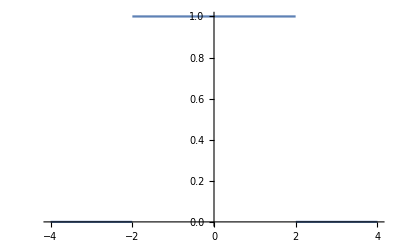

```mathematica
Plot[HeavisideTheta[(4-x^2)/4],{x,-4,4}]
```

```mathematica
∫_0^x (HeavisideTheta[1-r]*r^2)ⅆr
```

ConditionalExpression[1/3 (x^3 HeavisideTheta[-x]+HeavisideTheta[x]+(-1+x^3) HeavisideTheta[1-x,x]),x∈ℝ]

```mathematica
∫_(-∞)^∞ □ⅆ□
```

```mathematica
(4*π)/(√(2π))^3//FullSimplify
```

√(2/π)

```mathematica
FourierTransform[1/(1+(x^2+y^2+z^2)),{x,y,z},{κ,λ,ξ}]
```

$Aborted

```mathematica
InverseFourierTransform[1/(1+k^2),k,x]
```

(√(2/π))/(1-x^2)

```mathematica
FourierTransform[1/((x^2+y^2+z^2)-1),{x,y,z},{k,ω,λ}]
```

$Aborted

```mathematica
1/(√(2*π))^3*∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (ⅇ^(ⅈ*(k*x+j*y+l*z))/(k^2+j^2+l^2+κ^2))ⅆkⅆjⅆl
```

$Aborted

```mathematica
∫_(-∞)^∞ (ⅇ^(ⅈ*(k*x))/(k^2+j^2+l^2+κ^2))ⅆk
```

ConditionalExpression[(ⅇ^(-√(j^2+l^2+κ^2) Abs[x]) π)/(√(j^2+l^2+κ^2)),x∈ℝ&&√(-j^2-l^2-κ^2)≠0&&((√(-j^2-l^2-κ^2)∉ℝ&&(Re[j^2+l^2+κ^2]≥0||j^2+l^2+κ^2∉ℝ))||(Re[√(-j^2-l^2-κ^2)]≤0&&Re[j^2+l^2+κ^2]>0))]

```mathematica
∫_0^(2*π) (ⅇ^(ⅈ*r*Cos[ϕ]*Sin[θ]))ⅆϕ
```

ConditionalExpression[2 π BesselJ[0,r Sin[θ]],r Sin[θ]∈ℝ]

```mathematica
{x,y,z}.{r*Cos[ϕ]*Sin[θ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]}//FullSimplify
```

r (z Cos[θ]+Sin[θ] (x Cos[ϕ]+y Sin[ϕ]))

```mathematica
∫_0^π (ⅇ^(ⅈ*a*Cos[θ])*Sin[θ])ⅆθ
```

(2 Sin[a])/a

```mathematica
Laplacian[1/r*ⅇ^(-k*r),{r,θ,ϕ},"Spherical"]//FullSimplify
```

(ⅇ^(-k r) k^2)/r

```mathematica
∫_1^-1 (-ⅇ^(ⅈ*a*u))ⅆu//FullSimplify
```

(2 Sin[a])/a

```mathematica
∫_0^∞ ((r*Sin[a*r])/(r^2+k^2))ⅆr
```

ConditionalExpression[(√(a^2) π Cosh[a k]-ⅈ a (Log[-ⅈ a k]-Log[ⅈ a k]) Sinh[a k])/(2 a),(k∈ℝ||Re[k]≠0)&&Im[a]≤0]

```mathematica
∫_0^∞ (ⅇ^(k*r)*Sin[a*r])ⅆr
```

$Aborted

```mathematica
Assuming[Element[x,Reals]&&Element[κ,Reals],∫_0^∞ (Sin[r*x]*r/(r^2+κ^2))ⅆr]
```

1/2 ⅇ^(-Abs[x κ]) π Sign[x]

```mathematica
-k^2/(2*π*r)*ⅇ^(-k*r)-Laplacian[-1/(2*π*r)*ⅇ^(-k*r),{r,θ,ϕ},"Spherical"]//Simplify
```

0

```mathematica
4*π/Sqrt[2*π]^3
```

√(2/π)

```mathematica
2*π*ⅈ*(Residue[ⅇ^(ⅈ*r*x)*r/(r^2+κ^2),{r,ⅈ*κ}])
```

ⅈ ⅇ^(-x κ) π

```mathematica
?Residue
```

```mathematica
Sin[r*x]*r/(r^2+κ^2)
```

```mathematica
Laplacian[1/r*ⅇ^(-k*r),{r,θ,ϕ},"Spherical"]//FullSimplify
```

(ⅇ^(-k r) k^2)/r

```mathematica
Clear["Global*`"]
Assuming[Element[t,Reals]&&Element[d,Reals],∫_0^(2*π) ∫_0^t (r*ⅇ^(-ⅈ*d*r*Cos[θ]))ⅆrⅆθ]
```

$Aborted

```mathematica
∫_0^t (r*ⅇ^(-ⅈ*d*r*Cos[θ]))ⅆr//FullSimplify
```

(Sec[θ] (-Sec[θ]+ⅇ^(-ⅈ d t Cos[θ]) (ⅈ d t+Sec[θ])))/d^2

```mathematica
∫_0^(2*π) (Sec[θ] (-Sec[θ]+ⅇ^(-ⅈ d t Cos[θ]) (ⅈ d t+Sec[θ])))ⅆθ
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine::fas will be suppressed during this calculation.

∫_0^(2 π) Sec[θ] (-Sec[θ]+ⅇ^(-ⅈ d t Cos[θ]) (ⅈ d t+Sec[θ]))ⅆθ

```mathematica
∫HeavisideTheta[s-r]ⅆr
```

r+(-r+s) HeavisideTheta[r-s]

```mathematica
∫(1/r∫r*HeavisideTheta[s-r]ⅆr)ⅆr
```

1/4 (r^2+HeavisideTheta[r-s] (-r^2+s^2+2 s^2 Log[r]-2 s^2 Log[s]))

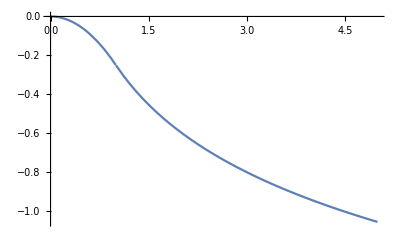

```mathematica
Plot[-1/4 (r^2+HeavisideTheta[r-1] (-r^2+1^2+2 1^2 (Log[r]-Log[1]))),{r,0,5}]
```

```mathematica
∫r*HeavisideTheta[s-r]ⅆr
```

1/2 (r^2+(-r^2+s^2) HeavisideTheta[r-s])

```mathematica
∫(r+(s^2/r-r)*HeavisideTheta[r-s])ⅆr
```

r^2/2+(-r^2/2+s^2/2) HeavisideTheta[r-s]+HeavisideTheta[r-s] (s^2 Log[r]-s^2 Log[s])

```mathematica
∫(x*HeavisideTheta[x-a])ⅆx
```

1/2 (-a^2+x^2) HeavisideTheta[-a+x]

```mathematica
∫(Cos[x]*HeavisideTheta[a-x])ⅆx
```

HeavisideTheta[-a+x] (Sin[a]-Sin[x])+Sin[x]

```mathematica
ϕ[r_]:=Piecewise[{{1/2-r^2/2,0<r<1},{Log[1/r],1<r}}];
Efield[r_]:=Piecewise[{{r,0<r<1},{1/r,1<r}}];
```

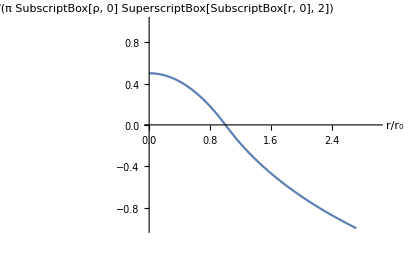

```mathematica
Plot[ϕ[r],{r,0,4},AxesLabel->{"r/r_0","(φ (r))/(π SubscriptBox[ρ, 0] SuperscriptBox[SubscriptBox[r, 0], 2])"},PlotRange->{{0,3},{-1,1}}]
```

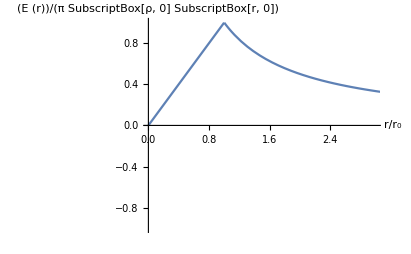

```mathematica
Plot[Efield[r],{r,0,4},AxesLabel->{"r/r_0","(E (r))/(π SubscriptBox[ρ, 0] SubscriptBox[r, 0])"},PlotRange->{{0,3},{-1,1}}]
```

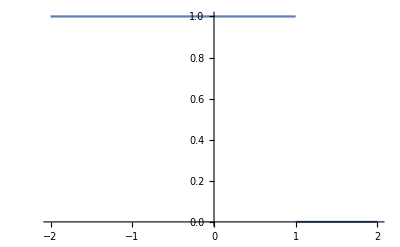

```mathematica
Plot[HeavisideTheta[1-x
],{x,-2,2}]
```

```mathematica
∫∫(HeavisideTheta[1-u^2])ⅆuⅆu//FullSimplify
```

1/2 (-(-1+u)^2 HeavisideTheta[-1+u]+(1+u)^2 HeavisideTheta[1+u])

```mathematica
(u+1)^2-(u-1)^2//FullSimplify
```

4 u

```mathematica
Assuming[Element[u,Reals]&&u>1,1/2 (-(-1+u)^2 HeavisideTheta[-1+u]+(1+u)^2 HeavisideTheta[1+u])]//FullSimplify
```

1/2 (-(-1+u)^2 HeavisideTheta[-1+u]+(1+u)^2 HeavisideTheta[1+u])

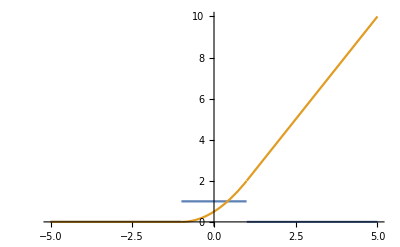

```mathematica
Plot[{HeavisideTheta[1-u^2],1/2 (-(-1+u)^2 HeavisideTheta[-1+u]+(1+u)^2 HeavisideTheta[1+u])},{u,-5,5}]
```

```mathematica
HeavisideTheta[0]//FullSimplify
```

HeavisideTheta[0]

```mathematica
?HeavisideTheta
```

```mathematica
φ[x_]:=Piecewise[{{x+1/2,x<-1/2},{1/4-x^2,-1/2<x<1/2},{1/2-x,x>1/2}}];
Erod[x_]:=Piecewise[{{-1,x<-1/2},{2*x,-1/2<x<1/2},{1,x>1/2}}];
```

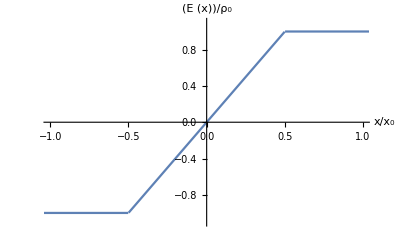

```mathematica
Plot[Erod[x],{x,-2,2},PlotRange->{{-1,1},{-1.1,1.1}},AxesLabel->{"x/x_0","(E (x))/ρ_0"}]
```

```mathematica
Series[1/(√(r^2-2*(XY)+y^2)),{XY,0,4}]
```

1/(√(r^2+y^2))+XY/((r^2+y^2)^(3/2))+(3 XY^2)/(2 (r^2+y^2)^(5/2))+(5 XY^3)/(2 (r^2+y^2)^(7/2))+(35 XY^4)/(8 (r^2+y^2)^(9/2))+O[XY]^5

```mathematica
Series[1/(√(1-2*X)),{X,0,5}]
```

1+X+(3 X^2)/2+(5 X^3)/2+(35 X^4)/8+(63 X^5)/8+O[X]^6

```mathematica
(Subscript[y, i]-Subscript[a, i])(Subscript[y, j]-Subscript[a, j])-Subscript[δ, ij](y-a)^2
```

(-a_i+y_i) (-a_j+y_j)-(-a+y)^2 δ_ij

```mathematica
(Subscript[y, i]-Subscript[a, i])*(Subscript[y, j]-Subscript[a, j])//FullSimplify
```

(a_i-y_i) (a_j-y_j)

```mathematica
yiyj+aiaj-yiaj-yjai
```

```mathematica
R=ImplicitRegion[(x/a)^2+(y/b)^2+(z/c)^2<1,{x,y,z}];
```

```mathematica
RegionMeasure[ImplicitRegion[(x/a)^2+(y/b)^2+(z/c)^2<1,{x,y,z}]]
```

0

```mathematica
Clear["Global`*"]
```

```mathematica
y[r_,θ_,ϕ_]:={a*r*Cos[ϕ]*Sin[θ],b*r*Sin[ϕ]*Sin[θ],c*r*Cos[θ]};
```

```mathematica
q[i_,j_,r_,θ_,ϕ_]:=(3*y[r,θ,ϕ][[i]]*y[r,θ,ϕ][[j]]-KroneckerDelta[i,j]*(y[r,θ,ϕ].y[r,θ,ϕ]));
```

```mathematica
Q1[i_,j_]:=ρ/2*∫_0^1 ∫_0^(2*π) ∫_0^π (q[i,j,r,θ,ϕ]*a*b*c*r^2*Sin[θ])ⅆθⅆϕⅆr
```

```mathematica
Table[Q1[i,j],{i,1,3},{j,1,3}]//FullSimplify//MatrixForm
```

(2/15 a b c (2 a^2-b^2-c^2) π ρ | 0 | 0
0 | -2/15 a b c (a^2-2 b^2+c^2) π ρ | 0
0 | 0 | -2/15 a b c (a^2+b^2-2 c^2) π ρ)

```mathematica
TeXForm[ Q1[1,1]+Q1[2,2]+Q1[3,3]]
```

-\frac{Q \left(a^2+b^2-2 c^2\right)}{10 a
   b c}+\frac{Q \left(2
   a^2-b^2-c^2\right)}{10 a b c}-\frac{Q
   \left(a^2-2 b^2+c^2\right)}{10 a b c}

```mathematica
TeXForm[Table[Q1[i,j],{i,1,3},{j,1,3}]//FullSimplify//MatrixForm]
```

\left(
\begin{array}{ccc}
 \frac{2}{15} \pi  a b c \rho  \left(2
   a^2-b^2-c^2\right) & 0 & 0 \\
 0 & -\frac{2}{15} \pi  a b c \rho 
   \left(a^2-2 b^2+c^2\right) & 0 \\
 0 & 0 & -\frac{2}{15} \pi  a b c \rho 
   \left(a^2+b^2-2 c^2\right) \\
\end{array}
\right)

```mathematica
v[r_,θ_,z_]:={r*Cos[θ],r*Sin[θ],z};
```

```mathematica
v[r,θ,z][[1]]*v[r,θ,z][[1]]//FullSimplify
```

r^2 Cos[θ]^2

```mathematica
∫_0^(2π) θ^2*Cos[θ+α]^2 ⅆθ
```

1/6 π (8 π^2+3 Cos[2 α]+6 π Sin[2 α])

```mathematica
(3*v[r,θ,z][[1]]*v[r,θ,z][[1]]-(KroneckerDelta[1,1]*(v[r,θ,z].v[r,θ,z])//FullSimplify))
```

-r^2-z^2+3 r^2 Cos[θ]^2

```mathematica
(3*v[r,θ,z][[2]]*v[r,θ,z][[2]]-(KroneckerDelta[2,2]*(v[r,θ,z].v[r,θ,z])//FullSimplify))
```

-r^2-z^2+3 r^2 Sin[θ]^2

```mathematica
Assuming[f[θ]== f[θ+α]&&Abs[α]<π,∫_0^(2*π) (f[θ]*Cos[θ]^2)ⅆθ]
```

∫_0^(2 π) Cos[θ]^2 f[θ]ⅆθ

```mathematica
∫_0^(2*π) (Cos[k*θ]*Sin[θ]^2)ⅆθ
```

-(2 Sin[2 k π])/(k (-4+k^2))

```mathematica
TeXForm[-r^2-z^2+3 r^2 Cos[θ]^2]
```

3 r^2 \cos ^2(\theta )-r^2-z^2

```mathematica
TeXForm[-r^2-z^2+3 r^2 Sin[θ]^2]
```

3 r^2 \sin ^2(\theta )-r^2-z^2

```mathematica
TeXForm[Series[(1-x)^(-1/2),{x,0,10}]]
```

1+\frac{x}{2}+\frac{3 x^2}{8}+\frac{5
   x^3}{16}+\frac{35 x^4}{128}+\frac{63
   x^5}{256}+\frac{231
   x^6}{1024}+\frac{429
   x^7}{2048}+\frac{6435
   x^8}{32768}+\frac{12155
   x^9}{65536}+\frac{46189
   x^{10}}{262144}+O\left(x^{11}\right)